```mathematica
rbar[r_,k_,t_]:=Mod[ModularInverse[k,t]*r,t,1]
```

```mathematica
secondOrder[r_,k_,t_,n_]:=PolyGamma[rbar[r,k,t^n]/t^n]/k-PolyGamma[r/t^n]
```

```mathematica
clicks={};
```

```mathematica
PlotEm[k_,t_,opts:OptionsPattern[ListPlot]]:=ListPlot[Table[{r/t,secondOrder[r,k,t]},{r,1,t}],opts]
```

```mathematica
PlotEmClicky[k_,t_,n_,opts:OptionsPattern[ListPlot]]:=Module[{data},
data=Table[{r/(t^n),secondOrder[r,k,t,n]},{r,1,t^n}];
Column[{ListPlot[Button[Tooltip@#,AppendTo[clicks,#]]&/@N@data,ImageSize->300],"\n\t",Row[{"clicks = ",Dynamic[clicks//TableForm]}]}]];
```

Show::gcomb: Could not combine the graphics objects in ….

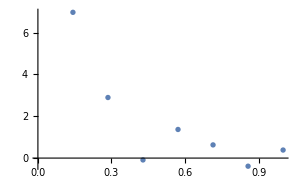
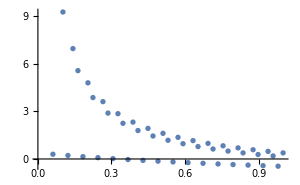
Show[-Graphics-

	
clicks = ,-Graphics-

	
clicks = ]

```mathematica
Show[PlotEm[3,7,1,PlotRange->All,PlotStyle->Red],PlotEm[3,7,2,PlotRange->All,PlotStyle->Blue]]
```

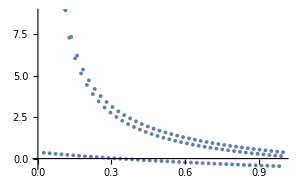
-Graphics-

	
clicks =

```mathematica
PlotEm[3,5,3,PlotRange->Automatic,PlotStyle->Red]
```

```mathematica
GetEmResidue[r_,k_,t_,n_]:=Module[{data},
data=Table[{(r+k*s)/(t^n),N[secondOrder[r+k*s,k,t,n]]},{s,0,Floor[(t^n-r)/k]}];
Return[data]
]
AllResidues[k_,t_,n_]:=Table[GetEmResidue[r,k,t,n],{r,1,k}]
```

```mathematica
AllResidues[8,5,2]
```

{{{1/25,25.414},{9/25,2.79135},{17/25,1.1974},{1,0.505064}},{{2/25,12.8202},{2/5,2.44076},{18/25,1.05504}},{{3/25,8.55346},{11/25,2.13412},{19/25,0.915129}},{{4/25,6.35745},{12/25,1.85388},{4/5,0.772431}},{{1/5,4.96887},{13/25,1.58132},{21/25,0.618204}},{{6/25,3.93572},{14/25,1.28561},{22/25,0.433908}},{{7/25,2.93968},{3/5,0.879489},{23/25,0.166334}},{{8/25,0.082583},{16/25,-0.216433},{24/25,-0.44609}}}

```mathematica
Map[First[#1]*5^3&,clicks]
```

{}

{14.,14.,14.,17.,17.,20.,23.,26.,29.,32.}

```mathematica
PlotInColor[k_,t_,n_,colors_:{Black,Red,Green,Blue,Orange}]:=Module[{data},
data=AllResidues[k,t,n];
ListPlot[data,PlotStyle->colors,PlotRange->Automatic,PlotLegends->Automatic]
]
```

Table::iterb: Iterator {r,1,5^(PlotStyle→GrayLevel[0])} does not have appropriate bounds.

Table::iterb: Iterator {r,1.,5.^(PlotStyle→GrayLevel[0.])} does not have appropriate bounds.

Table::nliter: Non-list iterator (#1&)[{r,1.,5.^(PlotStyle→GrayLevel[0.])}] at position 2 does not evaluate to a real numeric value.

ListPlot::lpn: … is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[,ListPlot[Table[(«1»&)[{Times[«2»],secondOrder[«4»]}],(«1»&)[{r,1.,Power[«2»]}]],ImageSize→300]

	
clicks = ].

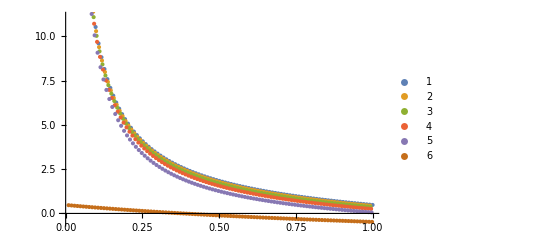
Show[-Graphics-,ListPlot[Table[(#1&)[{r/5.^(PlotStyle→GrayLevel[0.]),secondOrder[r,6.,5.,PlotStyle→GrayLevel[0.]]}],(#1&)[{r,1.,5.^(PlotStyle→GrayLevel[0.])}]],ImageSize→300]

	
clicks = ]

```mathematica
Show[PlotInColor[6,5,4,colors=Automatic],PlotEm[6,5,PlotStyle->Black]]
```

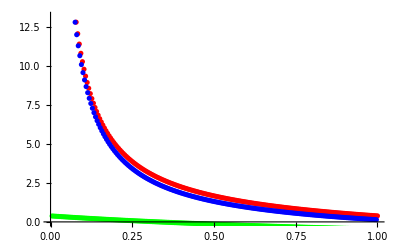

```mathematica
Show[PlotEmResidue[1,3,5,4,PlotRange->Automatic,PlotStyle->Red],PlotEmResidue[2,3,5,4,PlotRange->Automatic,PlotStyle->Blue],PlotEmResidue[3,3,5,4,PlotRange->Automatic,PlotStyle->Green]]
```

```mathematica
N[secondOrder[3,3,7,2]]
```

0.299398

```mathematica
N[secondOrder[4,3,7,1]]
```

1.36864